```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yinshi/Documents/work/post-doc-Humboldt/github/Moat-meanfield/MF_DR/renorm_finitep_v2/specfun/mub0/mu0data

```mathematica
mu=Table[i,{i,100,210,10}];
Re1=Table[Import["../T"<>ToString[mu[[i]]]<>"/Redata.dat"],{i,1,Length[mu]}];
Im1=Table[Import["../T"<>ToString[mu[[i]]]<>"/Imdata.dat"],{i,1,Length[mu]}];
omega=Table[i,{i,1,2001,10}];
p=Table[i,{i,10,2000,10}];
ϵ=0.2;
Re2=Table[Re1[[i]],{i,1,Length[mu]}];
Im2=Table[Table[Im1[[k]][[i]][[j]]-2ϵ omega[[j]],{i,1,201},{j,1,201}],{k,1,Length[mu]}];
spec=-1/π*Im2/(Re2^2+Im2^2);
```

```mathematica
ListPlot3D[spec[[5]],PlotRange->{All,All,{0,0.0000055}}]
```

-Graphics3D-

```mathematica
Dimensions[spec]
```

{12,201,201}

```mathematica
Table[Table[Export["./T"<>ToString[mu[[k]]]<>"/rho_data_p"<>ToString[i*10]<>".dat",spec[[k]][[i]]],{k,1,Length[mu]}],{i,1,Length[p]}];
```

```mathematica
data1=Flatten[Import["./T200/rho_data_p1.dat"]];
```

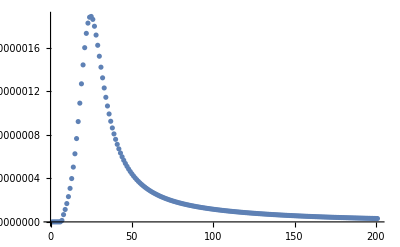

```mathematica
ListPlot[data1,PlotRange->All]
```